### Finger Counting

In the first chapter of  De temporum ratione, entitled "Calculating or Speaking with the Fingers," Bede described a form of finger counting known as flexus digitorum ("finger bending").  The practice of finger counting  dates back centuries, has been used by geographically separated disparate civilizations and varies in detail from culture to culture.  On page f. 33v from British Library Royal MS 13 (shown in the following illustration), an illuminator has provided a diagram accompanying Bede's textual description of how ancient Romans counted to 1,000 using their hands and fingers:

The Roman system of counting described by Bede remained in use for centuries, and a modified version of the system was presented by Luca Pacioli in his famous work Summa de arithmetica in 1494:

Bede introduced flexus digitorum as follows:

Before we begin, with God's help, to speak of chronology and its calculation, we deem it necessary first briefly to show the very necessary and ready skill in finger counting:
1: If you wish to say "one," you must bend the little finger of your left hand and place its tip on the palm;
2: for "two" lay down the ring finger next to it;
3: for "three" also the middle finger;
4: for "four" you must again raise the little finger;
5: for "five" also the ring finger;
6: for "six" you must extend the middle finger, and then the ring finger, which is called the medius, alone remains bent down upon the palm;
7: for "seven" extend all the fingers and bend only the little finger over the wrist;
8: for "eight" lay the ring finger down next to it;
9: for "nine" place the "impudent" (middle) finger next to it.

Menninger (2013, pp. 202–220) gives more details and additional historical context of the system of finger counting described by Bede, while also describing a number of variations employed by other cultures.

### Evagation

In chapter 26 of De temporum ratione, entitled, "Why the Moon, though Situated beneath the Sun, Sometimes Appears to Be above It," Bede uses evagation to explain apparent variations in the altitude of the Moon.  The term "evagation" refers to the variation of the north-south position of heavenly bodies relative to the ecliptic as they orbit, with their offsets expressed as musical ratios.  (It is noteworthy that in the chapter immediately following the discussion of evagation, Bede refers to the Pythagorean ratios of interplanetary distances as discussed by Pliny.)

Bede writes (as translated in Faith 1999, pp. 77–78):

It is no cause for marvel when we see that the Moon, as it passes through the southern signs, is much lower down and closer to the Earth than the Sun is when it tarries in its journey through these same regions. This is because the Moon travels within the frontier region separating this agitated atmosphere and the pure ether, for in fact it is much lower not only than the Sun, but also than Venus and Mercury, the lowest of the stars. Hence many philosophers say that the Sun's distance from the Moon is nineteen times the distance from the Moon to Earth. Pythagoras, a man of keen perception, deduced that it is 126,000 stadia from the Earth to the Moon, double that to the Sun, and three times that to the zodiac.

Evagations were also studied graphically.  For example, the Miscellany Works on Computus and Astronomy (Royal MS 13 A XI at the British Library) includes not only Bede's De temporum ratione and his earlier scientific treatises De natura rerum (On the Nature of Things) and De temporibus liber (On Times) composed in 703 CE, but also (on page f. 143v) a graph-like chart of the planets' orbits by Abbo of Fleury (d. 1004 CE):

-Graphics-

The drawing of such charts originates from one of the extracts from Pliny's Naturalis historia commonly found in cosmographical anthologies of this period.  Similar charts are also found, for example, in the cosmographical anthology known as Oxford, St. John's College MS 17 (Discenza 2017, p. 43):

While evagation diagrams were once hailed as the earliest appearance of a graph in European science, each planet's course was plotted independently since "the periods of their journeys through the zodiac cannot be reconciled" (The Calendar and the Cloister, Ch. 6, Sec. 9).

To see the phenomenon illustrated schematically in Abbo's plot, note that the north-south deviation of a celestial body from the ecliptic (the plane of Earth's orbit around the Sun) is termed the ecliptic latitude (also called the celestial latitude).  Using data from the Wolfram Knowledgebase on planets and planetary moons:

```mathematica
EclipticLatitudeData[body_,prop_,dr_]:=TimeSeries[Transpose[{dr,QuantityMagnitude[body[Dated[prop,#]&/@dr],"AngularDegrees"]}]]
```

… allows the actual plot of angular deviation from the ecliptic to be plotted  (in degrees) for the Moon as a function of date:

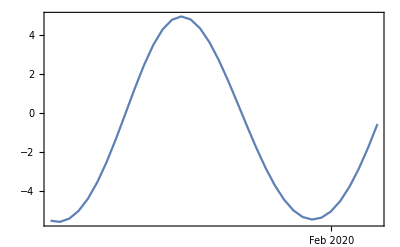

```mathematica
DateListPlot[EclipticLatitudeData[Entity["PlanetaryMoon","Moon"],"GeocentricEclipticLatitude",DateRange[DateObject[{2020,1,2},"Day","Gregorian",-4.],DateObject[{2020,2,5},"Day","Gregorian",-4.]]]]
```

A similar plot may be made for Mars.  Using the ecliptic latitude with respect to the Sun gives a smooth-looking plot:

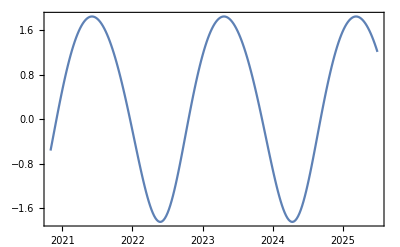

```mathematica
DateListPlot[EclipticLatitudeData[Entity["Planet","Mars"],"HeliocentricEclipticLatitude",DateRange[DateObject[{2020,11,1},"Day","Gregorian",-4.],DateObject[{2025,7,1},"Day","Gregorian",-4.],Quantity[1, "Weeks"]]]]
```

However, the analogous plot using ecliptic latitude with respect to Earth is more irregular:

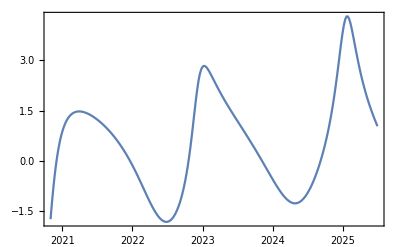

```mathematica
DateListPlot[EclipticLatitudeData[Entity["Planet","Mars"],"GeocentricEclipticLatitude",DateRange[DateObject[{2020,11,1},"Day","Gregorian",-4.],DateObject[{2025,7,1},"Day","Gregorian",-4.],Quantity[1, "Weeks"]]]]
```

While the scales and curvature of such plots are different from those shown in Abbo's evagation diagram, the general characteristics of near-periodic oscillations about the ecliptic plane shown in his diagram are present.